```mathematica
f[x_]:=(x-γ)^2+γ+m;
p1[x_]:=(x-γ)^4+d(x-γ)^3+c(x-γ)^2+b(x-γ)+a;
p2[x_]:=(x-γ)^4-d(x-γ)^3+c(x-γ)^2-b(x-γ)+a;
```

```mathematica
Collect[f[f[f[x]]],x-γ]
```

m+m^2+2 m^3+m^4+(4 m^2+4 m^3) (x-γ)^2+(2 m+6 m^2) (x-γ)^4+4 m (x-γ)^6+(x-γ)^8+γ

```mathematica
Collect[p1[x]p2[x],x-γ]
```

a^2+(-b^2+2 a c) (x-γ)^2+(2 a+c^2-2 b d) (x-γ)^4+(2 c-d^2) (x-γ)^6+(x-γ)^8

```mathematica
sys={m+m^2+2 m^3+m^4+γ==a^2,
4 m^2+4 m^3==-b^2+2 a c,
2 m+6 m^2==2 a+c^2-2 b d,
4 m==2 c-d^2};
sys//TableForm
```

m+m^2+2 m^3+m^4+γ==a^2
4 m^2+4 m^3==-b^2+2 a c
2 m+6 m^2==2 a+c^2-2 b d
4 m==2 c-d^2

```mathematica
Clear[a,b,c,d]
```

```mathematica
a=Solve[sys[[2]],a][[1,1,2]];
b=Solve[sys[[3]],b][[1,1,2]];
c=Solve[sys[[4]],c][[1,1,2]];
```

{{γ→-m-m^2-2 m^3-m^4+1/((d^2+4 m)^2)(4 m^2+4 m^3+(1/2 d (d^2+4 m)-√(-4 m^2-4 m^3+m (d^2+4 m)+3 m^2 (d^2+4 m)+1/4 d^2 (d^2+4 m)^2-1/8 (d^2+4 m)^3))^2)^2}}

```mathematica
Solve[sys[[1]],γ]//FullSimplify
```

{{γ→-m-m^2-2 m^3-m^4+1/64 (3 d^4+8 d^2 m+8 m (1+m)-2 √2 d √(d^6+4 d^4 m+8 d^2 m (1+m)))^2}}

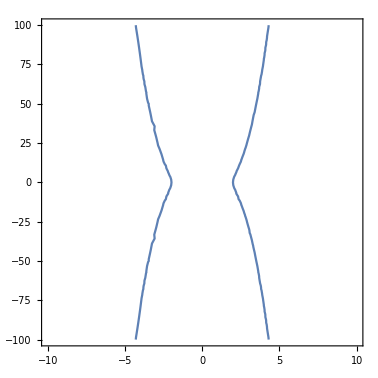

```mathematica
ContourPlot[y^2==2(d^6+4 d^4 m+8 d^2 m (1+m)),{d,-10,10},{y,-100,100}]
```

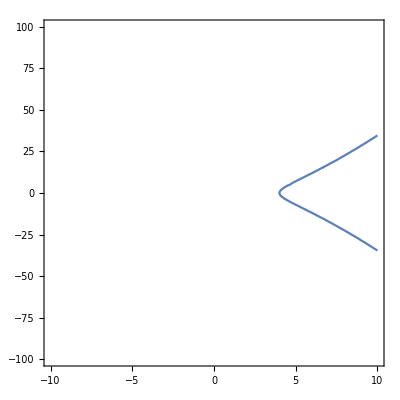

```mathematica
ContourPlot[y^2==2(d^3+4 d^2 m+8 m (1+m)),{d,-10,10},{y,-100,100}]
```

```mathematica
Clear[y,d,m];
FindInstance[y^2==2(d^3+4 d^2 m+8 m (1+m))&&y≠0,{y,d,m},Integers]
```

{{y→4,d→2,m→-3}}